```mathematica
Clear[FormatAdjacencyMatrix3];
```

```mathematica
FormatAdjacencyMatrix3[g_,sym_,highligh_:{},main_:{}]:=Block[{vertices=Sort[VertexList[g]],mat, value,sets,sets2,mat2,labels,colors,vertexpos=Association[]},
mat=Table[
Table[
value=If[i==j,"◆",If[EdgeQ[g,i<->j],Style["●",Darker[Green]],Style["●",Darker[Red]]]];
If[MemberQ[highligh,i]||MemberQ[highligh,j],Framed[value,FrameMargins->None,FrameStyle->Gray],value]
,{j,vertices}
]
,{i,vertices}
];
sets=SymbolToSets[sym];
Table[vertexpos[vertices[[i]]]=i,{i,Length[VertexList[g]]}];
sets2=Flatten[sets];
sets2=Join[sets2,SetDifference[VertexList[g],sets2]];
colors=Association[SymbolToColoring[sym]];
labels=Map[With[{base=If[KeyExistsQ[colors,#],Style[#,Darker[colors[#]]],Style[#,Bold]]},
If[MemberQ[main,#],Framed[base],#]]&,sets2];
mat2=Table[Table[mat[[vertexpos[sets2[[i]]],vertexpos[sets2[[j]]]]],{i,Length[mat]}],{j,Length[mat]}];
MatrixForm[mat2,
TableHeadings->{labels,Map[Rotate[#,-Pi/2]&,labels]}]
]
```

```mathematica
MatchGraph[with_,contract_]:=Block[{vertices=Join[with,contract],ws1,cs1,edges={}},
Table[
ws1=SymbolToSets[w1];
Table[
cs1=SymbolToSets[c1];
If[PartitionHasPatternFast[ws1,cs1],
AppendTo[edges,w1->c1]
];
,
{c1,contract}
],
{w1,with}
];
With[
{g=Graph[edges,GraphLayout->"BipartiteEmbedding", ImageSize->300]},
Graph[g,VertexLabels->Map[Rotate[SymbolToLabel[#],Pi/5]&,VertexList[g]]]
]
];
```

```mathematica
MpgChainMat[g_]:=Block[{mpgs,formula,neigh, neigh1, neigh2,both,fcontract, found={}, uniqueEdges={},exists,fullf},
mpgs=Map[SortEdge,CollectMPGEdges[g]];
Table[With[{contract=EdgeContract[g,e]},
exists=Select[found,IsomorphicGraphQ[contract,#]&];
If[exists=={},
AppendTo[uniqueEdges,e];
AppendTo[found,contract]
]
],
{e,Reverse[mpgs]}
];
Table[
With[{contract=EdgeContract[g,e]},
fcontract=FindFullFormula4[contract];
formula=First[fcontract];
neigh1=VertexList[NeighborhoodGraph[g,e[[1]]]];
neigh2=VertexList[NeighborhoodGraph[g,e[[2]]]];
neigh=Union[neigh1,neigh2];
both=Intersection[neigh1,neigh2];
fullf=FindFullFormula4[g];
Labeled[
FormatAdjacencyMatrix3[g,formula,neigh, both],
{e,neigh,Column[ fullf]}
]
->
Labeled[FormatAdjacencyMatrix3[VertexAdd[contract,e[[2]]],formula,neigh,both],Column[Sort[fcontract]]]
->
MatchGraph[fullf,fcontract]
],
{e,uniqueEdges}
]
]
```

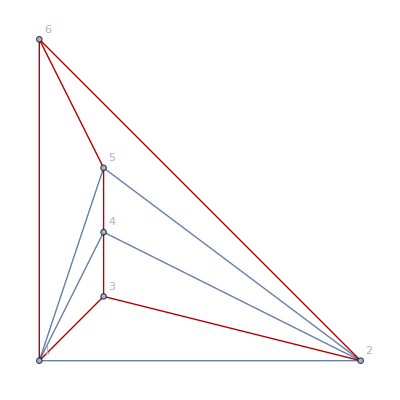

```mathematica
With[{g=MinimalGraph[5]},Graph[g,VertexLabels->"Name",GraphLayout->"PlanarEmbedding",GraphHighlight->CollectMPGEdges[g],GraphHighlightStyle->"Thick"]]
```

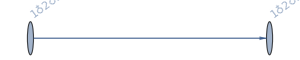
{( | 1 | 2 | 3 | 5 | 7 | 4 | 6 | 8
1 | ◆ | ● | ● | ● | ● | ● | ● | ●
2 | ● | ◆ | ● | ● | ● | ● | ● | ●
3 | ● | ● | ◆ | ● | ● | ● | ● | ●
5 | ● | ● | ● | ◆ | ● | ● | ● | ●
7 | ● | ● | ● | ● | ◆ | ● | ● | ●
4 | ● | ● | ● | ● | ● | ◆ | ● | ●
6 | ● | ● | ● | ● | ● | ● | ◆ | ●
8 | ● | ● | ● | ● | ● | ● | ● | ◆){7<->8,{1,2,6,7,8},v1x2x357x468}→( | 1 | 2 | 3 | 5 | 7 | 4 | 6 | 8
1 | ◆ | ● | ● | ● | ● | ● | ● | ●
2 | ● | ◆ | ● | ● | ● | ● | ● | ●
3 | ● | ● | ◆ | ● | ● | ● | ● | ●
5 | ● | ● | ● | ◆ | ● | ● | ● | ●
7 | ● | ● | ● | ● | ◆ | ● | ● | ●
4 | ● | ● | ● | ● | ● | ◆ | ● | ●
6 | ● | ● | ● | ● | ● | ● | ◆ | ●
8 | ● | ● | ● | ● | ● | ● | ● | ◆)v1x2x357x46→-Graphics-}

```mathematica
MpgChainMat[MinimalGraph[7]]
```

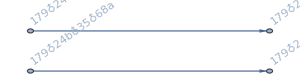
{( | 1 | 11 | 2 | 5 | 9 | 3 | 7 | 10 | 4 | 6 | 8 | 12
1 | ◆ | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ●
11 | ● | ◆ | ● | ● | ● | ● | ● | ● | ● | ● | ● | ●
2 | ● | ● | ◆ | ● | ● | ● | ● | ● | ● | ● | ● | ●
5 | ● | ● | ● | ◆ | ● | ● | ● | ● | ● | ● | ● | ●
9 | ● | ● | ● | ● | ◆ | ● | ● | ● | ● | ● | ● | ●
3 | ● | ● | ● | ● | ● | ◆ | ● | ● | ● | ● | ● | ●
7 | ● | ● | ● | ● | ● | ● | ◆ | ● | ● | ● | ● | ●
10 | ● | ● | ● | ● | ● | ● | ● | ◆ | ● | ● | ● | ●
4 | ● | ● | ● | ● | ● | ● | ● | ● | ◆ | ● | ● | ●
6 | ● | ● | ● | ● | ● | ● | ● | ● | ● | ◆ | ● | ●
8 | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ◆ | ●
12 | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ◆){11<->12,{5,6,7,8,9,10,11,12},v19bx25cx37ax468
v19bx24cx357x68a
v18ax29bx357x46c
v18bx259x37ax46c
v18bx24cx36ax579
v18ax24bx36cx579
v17ax29bx35cx468
v17ax259x36cx48b
v179x25cx36ax48b
v179x24bx35cx68a}→( | 1 | 11 | 2 | 5 | 9 | 3 | 7 | 10 | 4 | 6 | 8 | 12
1 | ◆ | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ●
11 | ● | ◆ | ● | ● | ● | ● | ● | ● | ● | ● | ● | ●
2 | ● | ● | ◆ | ● | ● | ● | ● | ● | ● | ● | ● | ●
5 | ● | ● | ● | ◆ | ● | ● | ● | ● | ● | ● | ● | ●
9 | ● | ● | ● | ● | ◆ | ● | ● | ● | ● | ● | ● | ●
3 | ● | ● | ● | ● | ● | ◆ | ● | ● | ● | ● | ● | ●
7 | ● | ● | ● | ● | ● | ● | ◆ | ● | ● | ● | ● | ●
10 | ● | ● | ● | ● | ● | ● | ● | ◆ | ● | ● | ● | ●
4 | ● | ● | ● | ● | ● | ● | ● | ● | ◆ | ● | ● | ●
6 | ● | ● | ● | ● | ● | ● | ● | ● | ● | ◆ | ● | ●
8 | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ◆ | ●
12 | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ◆)v179x24bx35x68a
v179x24bx36ax58
v17ax259x3bx468
v18ax24bx357x69
v18ax24bx36x579
v18x24bx36ax579
v19x24bx357x68a
v1bx259x37ax468→-Graphics-}

```mathematica
MpgChainMat[Graph[plantri[[1]]]]
```

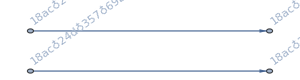
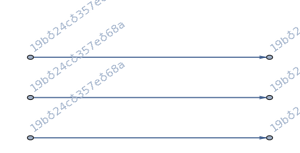
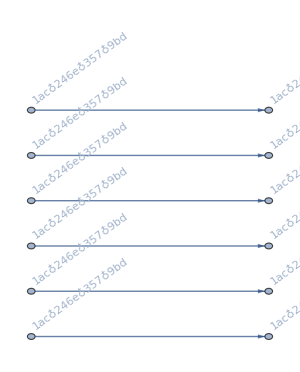
{( | 1 | 13 | 2 | 5 | 10 | 3 | 6 | 8 | 11 | 4 | 7 | 9 | 12 | 14
1 | ◆ | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ●
13 | ● | ◆ | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ●
2 | ● | ● | ◆ | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ●
5 | ● | ● | ● | ◆ | ● | ● | ● | ● | ● | ● | ● | ● | ● | ●
10 | ● | ● | ● | ● | ◆ | ● | ● | ● | ● | ● | ● | ● | ● | ●
3 | ● | ● | ● | ● | ● | ◆ | ● | ● | ● | ● | ● | ● | ● | ●
6 | ● | ● | ● | ● | ● | ● | ◆ | ● | ● | ● | ● | ● | ● | ●
8 | ● | ● | ● | ● | ● | ● | ● | ◆ | ● | ● | ● | ● | ● | ●
11 | ● | ● | ● | ● | ● | ● | ● | ● | ◆ | ● | ● | ● | ● | ●
4 | ● | ● | ● | ● | ● | ● | ● | ● | ● | ◆ | ● | ● | ● | ●
7 | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ◆ | ● | ● | ●
9 | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ◆ | ● | ●
12 | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ◆ | ●
14 | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ◆){13<->14,{6,7,8,9,10,11,12,13,14},v1ex25adx368bx479c
v1adx25ex368bx479c
v19bdx2acx357ex468
v19bdx26ax357ex48c
v19cx25adx368bx47e
v19bdx246ex38cx57a
v19bdx246ex37cx58a
v19bdx246x357ex8ac
v19bdx246ex357x8ac
v19bdx246ex358x7ac
v19bdx24cx357ex68a
v18acx2bdx357ex469
v18acx26bx357ex49d
v18bx25adx36ex479c
v18acx246ex3bdx579
v18acx246ex37bx59d
v18acx246x357ex9bd
v18acx246ex357x9bd
v18acx246ex35dx79b
v18acx24dx357ex69b}→( | 1 | 13 | 2 | 5 | 10 | 3 | 6 | 8 | 11 | 4 | 7 | 9 | 12 | 14
1 | ◆ | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ●
13 | ● | ◆ | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ●
2 | ● | ● | ◆ | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ●
5 | ● | ● | ● | ◆ | ● | ● | ● | ● | ● | ● | ● | ● | ● | ●
10 | ● | ● | ● | ● | ◆ | ● | ● | ● | ● | ● | ● | ● | ● | ●
3 | ● | ● | ● | ● | ● | ◆ | ● | ● | ● | ● | ● | ● | ● | ●
6 | ● | ● | ● | ● | ● | ● | ◆ | ● | ● | ● | ● | ● | ● | ●
8 | ● | ● | ● | ● | ● | ● | ● | ◆ | ● | ● | ● | ● | ● | ●
11 | ● | ● | ● | ● | ● | ● | ● | ● | ◆ | ● | ● | ● | ● | ●
4 | ● | ● | ● | ● | ● | ● | ● | ● | ● | ◆ | ● | ● | ● | ●
7 | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ◆ | ● | ● | ●
9 | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ◆ | ● | ●
12 | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ◆ | ●
14 | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ◆)v18acx246x35dx79b
v18acx24dx357x69b
v18acx24dx36bx579
v18acx25dx36bx479
v18acx25dx37bx469
v18acx26bx35dx479
v18ax25dx36bx479c
v18ax26bx35dx479c
v18bx26ax35dx479c
v19cx24dx368bx57a
v1acx24dx368bx579
v1acx25dx368bx479
v1ax25dx368bx479c
v1dx25ax368bx479c→-Graphics-,( | 1 | 10 | 12 | 2 | 5 | 14 | 3 | 6 | 8 | 11 | 4 | 7 | 9 | 13
1 | ◆ | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ●
10 | ● | ◆ | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ●
12 | ● | ● | ◆ | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ●
2 | ● | ● | ● | ◆ | ● | ● | ● | ● | ● | ● | ● | ● | ● | ●
5 | ● | ● | ● | ● | ◆ | ● | ● | ● | ● | ● | ● | ● | ● | ●
14 | ● | ● | ● | ● | ● | ◆ | ● | ● | ● | ● | ● | ● | ● | ●
3 | ● | ● | ● | ● | ● | ● | ◆ | ● | ● | ● | ● | ● | ● | ●
6 | ● | ● | ● | ● | ● | ● | ● | ◆ | ● | ● | ● | ● | ● | ●
8 | ● | ● | ● | ● | ● | ● | ● | ● | ◆ | ● | ● | ● | ● | ●
11 | ● | ● | ● | ● | ● | ● | ● | ● | ● | ◆ | ● | ● | ● | ●
4 | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ◆ | ● | ● | ●
7 | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ◆ | ● | ●
9 | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ◆ | ●
13 | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ◆){12<->13,{5,6,7,8,11,12,13,14},v1ex25adx368bx479c
v1adx25ex368bx479c
v19bdx2acx357ex468
v19bdx26ax357ex48c
v19cx25adx368bx47e
v19bdx246ex38cx57a
v19bdx246ex37cx58a
v19bdx246x357ex8ac
v19bdx246ex357x8ac
v19bdx246ex358x7ac
v19bdx24cx357ex68a
v18acx2bdx357ex469
v18acx26bx357ex49d
v18bx25adx36ex479c
v18acx246ex3bdx579
v18acx246ex37bx59d
v18acx246x357ex9bd
v18acx246ex357x9bd
v18acx246ex35dx79b
v18acx24dx357ex69b}→( | 1 | 10 | 12 | 2 | 5 | 14 | 3 | 6 | 8 | 11 | 4 | 7 | 9 | 13
1 | ◆ | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ●
10 | ● | ◆ | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ●
12 | ● | ● | ◆ | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ●
2 | ● | ● | ● | ◆ | ● | ● | ● | ● | ● | ● | ● | ● | ● | ●
5 | ● | ● | ● | ● | ◆ | ● | ● | ● | ● | ● | ● | ● | ● | ●
14 | ● | ● | ● | ● | ● | ◆ | ● | ● | ● | ● | ● | ● | ● | ●
3 | ● | ● | ● | ● | ● | ● | ◆ | ● | ● | ● | ● | ● | ● | ●
6 | ● | ● | ● | ● | ● | ● | ● | ◆ | ● | ● | ● | ● | ● | ●
8 | ● | ● | ● | ● | ● | ● | ● | ● | ◆ | ● | ● | ● | ● | ●
11 | ● | ● | ● | ● | ● | ● | ● | ● | ● | ◆ | ● | ● | ● | ●
4 | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ◆ | ● | ● | ●
7 | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ◆ | ● | ●
9 | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ◆ | ●
13 | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ◆)v18ax24cx357ex69b
v18ax26bx357ex49c
v18bx26ax357ex49c
v18bx2acx357ex469
v19bx24cx357ex68a
v19bx2acx357ex468
v19cx246ex37bx58a
v19cx246ex38bx57a
v19cx24ex368bx57a
v19cx25ax368bx47e
v1acx246ex358x79b
v1acx246ex38bx579
v1acx24ex368bx579
v1acx25ex368bx479→-Graphics-,( | 1 | 10 | 12 | 2 | 4 | 6 | 14 | 3 | 7 | 11 | 5 | 9 | 13 | 8
1 | ◆ | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ●
10 | ● | ◆ | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ●
12 | ● | ● | ◆ | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ●
2 | ● | ● | ● | ◆ | ● | ● | ● | ● | ● | ● | ● | ● | ● | ●
4 | ● | ● | ● | ● | ◆ | ● | ● | ● | ● | ● | ● | ● | ● | ●
6 | ● | ● | ● | ● | ● | ◆ | ● | ● | ● | ● | ● | ● | ● | ●
14 | ● | ● | ● | ● | ● | ● | ◆ | ● | ● | ● | ● | ● | ● | ●
3 | ● | ● | ● | ● | ● | ● | ● | ◆ | ● | ● | ● | ● | ● | ●
7 | ● | ● | ● | ● | ● | ● | ● | ● | ◆ | ● | ● | ● | ● | ●
11 | ● | ● | ● | ● | ● | ● | ● | ● | ● | ◆ | ● | ● | ● | ●
5 | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ◆ | ● | ● | ●
9 | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ◆ | ● | ●
13 | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ◆ | ●
8 | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ◆){7<->8,{1,2,6,7,8,9,13,14},v1ex25adx368bx479c
v1adx25ex368bx479c
v19bdx2acx357ex468
v19bdx26ax357ex48c
v19cx25adx368bx47e
v19bdx246ex38cx57a
v19bdx246ex37cx58a
v19bdx246x357ex8ac
v19bdx246ex357x8ac
v19bdx246ex358x7ac
v19bdx24cx357ex68a
v18acx2bdx357ex469
v18acx26bx357ex49d
v18bx25adx36ex479c
v18acx246ex3bdx579
v18acx246ex37bx59d
v18acx246x357ex9bd
v18acx246ex357x9bd
v18acx246ex35dx79b
v18acx24dx357ex69b}→( | 1 | 10 | 12 | 2 | 4 | 6 | 14 | 3 | 7 | 11 | 5 | 9 | 13 | 8
1 | ◆ | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ●
10 | ● | ◆ | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ●
12 | ● | ● | ◆ | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ●
2 | ● | ● | ● | ◆ | ● | ● | ● | ● | ● | ● | ● | ● | ● | ●
4 | ● | ● | ● | ● | ◆ | ● | ● | ● | ● | ● | ● | ● | ● | ●
6 | ● | ● | ● | ● | ● | ◆ | ● | ● | ● | ● | ● | ● | ● | ●
14 | ● | ● | ● | ● | ● | ● | ◆ | ● | ● | ● | ● | ● | ● | ●
3 | ● | ● | ● | ● | ● | ● | ● | ◆ | ● | ● | ● | ● | ● | ●
7 | ● | ● | ● | ● | ● | ● | ● | ● | ◆ | ● | ● | ● | ● | ●
11 | ● | ● | ● | ● | ● | ● | ● | ● | ● | ◆ | ● | ● | ● | ●
5 | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ◆ | ● | ● | ●
9 | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ◆ | ● | ●
13 | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ◆ | ●
8 | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ◆)v19bdx246ex357xac
v19bdx246ex35x7ac
v19bdx246ex37cx5a
v19bdx246ex3cx57a
v19bdx246x35ex7ac
v19bdx24cx36ex57a
v19bdx25ax36ex47c
v19bdx25ax37cx46e
v19bdx26ax35ex47c
v19bdx2acx357x46e
v19bx246ex35dx7ac
v19bx246ex37cx5ad
v19bx25adx36ex47c
v19bx25adx37cx46e
v19cx246ex37bx5ad
v19cx246ex3bdx57a
v19cx25adx37bx46e
v1acx246ex357x9bd
v1acx246ex37bx59d→-Graphics-}

```mathematica
MpgChainMat[Graph[plantri[[2]]]]
```

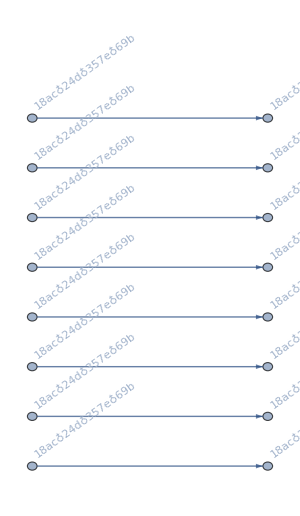
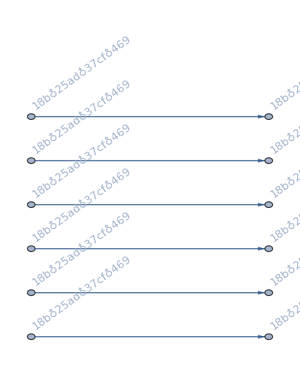
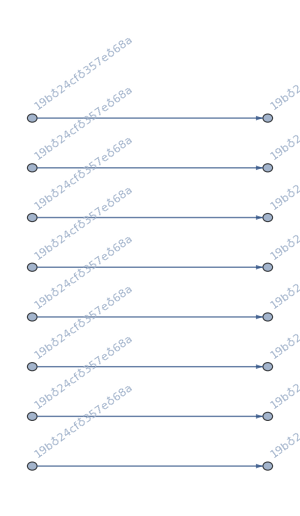
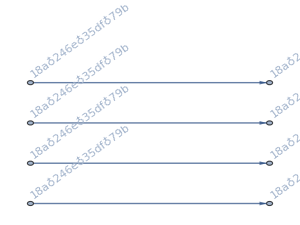
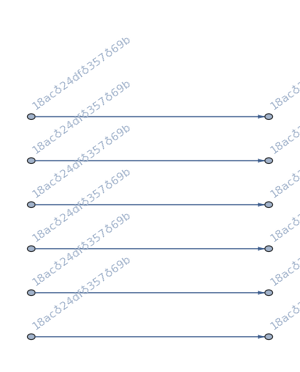
{( | 1 | 14 | 2 | 5 | 10 | 13 | 3 | 6 | 8 | 11 | 4 | 7 | 9 | 12 | 15
1 | ◆ | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ●
14 | ● | ◆ | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ●
2 | ● | ● | ◆ | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ●
5 | ● | ● | ● | ◆ | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ●
10 | ● | ● | ● | ● | ◆ | ● | ● | ● | ● | ● | ● | ● | ● | ● | ●
13 | ● | ● | ● | ● | ● | ◆ | ● | ● | ● | ● | ● | ● | ● | ● | ●
3 | ● | ● | ● | ● | ● | ● | ◆ | ● | ● | ● | ● | ● | ● | ● | ●
6 | ● | ● | ● | ● | ● | ● | ● | ◆ | ● | ● | ● | ● | ● | ● | ●
8 | ● | ● | ● | ● | ● | ● | ● | ● | ◆ | ● | ● | ● | ● | ● | ●
11 | ● | ● | ● | ● | ● | ● | ● | ● | ● | ◆ | ● | ● | ● | ● | ●
4 | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ◆ | ● | ● | ● | ●
7 | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ◆ | ● | ● | ●
9 | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ◆ | ● | ●
12 | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ◆ | ●
15 | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ◆){14<->15,{8,9,10,11,12,13,14,15},v1dfx25aex368bx479c
v1cfx25adx368bx479e
v1acx25dfx368bx479e
v1aex25dfx368bx479c
v1acx24dfx368bx579e
v1adx24cfx368bx579e
v19bdx26aex357fx48c
v19bdx26aex358x47cf
v19bdx25aex37cfx468
v19bdx25aex368x47cf
v19dx25aex368bx47cf
v19ex25adx368bx47cf
v19bdx246fx38cx57ae
v19bdx246ex37cfx58a
v19bdx24cfx368x57ae
v19cx24dfx368bx57ae
v19dx24cfx368bx57ae
v19bdx246fx357ex8ac
v19bdx246ex357fx8ac
v19bdx24cfx357ex68a
v18acx2bdx357fx469e
v18acx26bx35dfx479e
v18bx26aex35dfx479c
v18bx25adx37cfx469e
v18acx25dfx37bx469e
v18acx25dfx36bx479e
v18acx246fx3bdx579e
v18acx24dfx36bx579e
v18acx246fx357ex9bd
v18acx246ex357fx9bd
v18acx246ex35dfx79b
v18acx24dfx357ex69b}→( | 1 | 14 | 2 | 5 | 10 | 13 | 3 | 6 | 8 | 11 | 4 | 7 | 9 | 12 | 15
1 | ◆ | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ●
14 | ● | ◆ | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ●
2 | ● | ● | ◆ | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ●
5 | ● | ● | ● | ◆ | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ●
10 | ● | ● | ● | ● | ◆ | ● | ● | ● | ● | ● | ● | ● | ● | ● | ●
13 | ● | ● | ● | ● | ● | ◆ | ● | ● | ● | ● | ● | ● | ● | ● | ●
3 | ● | ● | ● | ● | ● | ● | ◆ | ● | ● | ● | ● | ● | ● | ● | ●
6 | ● | ● | ● | ● | ● | ● | ● | ◆ | ● | ● | ● | ● | ● | ● | ●
8 | ● | ● | ● | ● | ● | ● | ● | ● | ◆ | ● | ● | ● | ● | ● | ●
11 | ● | ● | ● | ● | ● | ● | ● | ● | ● | ◆ | ● | ● | ● | ● | ●
4 | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ◆ | ● | ● | ● | ●
7 | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ◆ | ● | ● | ●
9 | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ◆ | ● | ●
12 | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ◆ | ●
15 | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ◆)v18acx246ex357x9bd
v18acx246ex35dx79b
v18acx246ex37bx59d
v18acx246ex3bdx579
v18acx246x357ex9bd
v18acx24dx357ex69b
v18acx26bx357ex49d
v18acx2bdx357ex469
v18bx25adx36ex479c
v19bdx246ex357x8ac
v19bdx246ex358x7ac
v19bdx246ex37cx58a
v19bdx246ex38cx57a
v19bdx246x357ex8ac
v19bdx24cx357ex68a
v19bdx26ax357ex48c
v19bdx2acx357ex468
v19cx25adx368bx47e
v1adx25ex368bx479c
v1ex25adx368bx479c→-Graphics-,( | 1 | 15 | 2 | 5 | 10 | 13 | 3 | 6 | 8 | 11 | 4 | 7 | 9 | 12 | 14
1 | ◆ | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ●
15 | ● | ◆ | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ●
2 | ● | ● | ◆ | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ●
5 | ● | ● | ● | ◆ | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ●
10 | ● | ● | ● | ● | ◆ | ● | ● | ● | ● | ● | ● | ● | ● | ● | ●
13 | ● | ● | ● | ● | ● | ◆ | ● | ● | ● | ● | ● | ● | ● | ● | ●
3 | ● | ● | ● | ● | ● | ● | ◆ | ● | ● | ● | ● | ● | ● | ● | ●
6 | ● | ● | ● | ● | ● | ● | ● | ◆ | ● | ● | ● | ● | ● | ● | ●
8 | ● | ● | ● | ● | ● | ● | ● | ● | ◆ | ● | ● | ● | ● | ● | ●
11 | ● | ● | ● | ● | ● | ● | ● | ● | ● | ◆ | ● | ● | ● | ● | ●
4 | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ◆ | ● | ● | ● | ●
7 | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ◆ | ● | ● | ●
9 | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ◆ | ● | ●
12 | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ◆ | ●
14 | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ◆){13<->14,{6,7,8,11,12,13,14,15},v1dfx25aex368bx479c
v1cfx25adx368bx479e
v1acx25dfx368bx479e
v1aex25dfx368bx479c
v1acx24dfx368bx579e
v1adx24cfx368bx579e
v19bdx26aex357fx48c
v19bdx26aex358x47cf
v19bdx25aex37cfx468
v19bdx25aex368x47cf
v19dx25aex368bx47cf
v19ex25adx368bx47cf
v19bdx246fx38cx57ae
v19bdx246ex37cfx58a
v19bdx24cfx368x57ae
v19cx24dfx368bx57ae
v19dx24cfx368bx57ae
v19bdx246fx357ex8ac
v19bdx246ex357fx8ac
v19bdx24cfx357ex68a
v18acx2bdx357fx469e
v18acx26bx35dfx479e
v18bx26aex35dfx479c
v18bx25adx37cfx469e
v18acx25dfx37bx469e
v18acx25dfx36bx479e
v18acx246fx3bdx579e
v18acx24dfx36bx579e
v18acx246fx357ex9bd
v18acx246ex357fx9bd
v18acx246ex35dfx79b
v18acx24dfx357ex69b}→( | 1 | 15 | 2 | 5 | 10 | 13 | 3 | 6 | 8 | 11 | 4 | 7 | 9 | 12 | 14
1 | ◆ | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ●
15 | ● | ◆ | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ●
2 | ● | ● | ◆ | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ●
5 | ● | ● | ● | ◆ | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ●
10 | ● | ● | ● | ● | ◆ | ● | ● | ● | ● | ● | ● | ● | ● | ● | ●
13 | ● | ● | ● | ● | ● | ◆ | ● | ● | ● | ● | ● | ● | ● | ● | ●
3 | ● | ● | ● | ● | ● | ● | ◆ | ● | ● | ● | ● | ● | ● | ● | ●
6 | ● | ● | ● | ● | ● | ● | ● | ◆ | ● | ● | ● | ● | ● | ● | ●
8 | ● | ● | ● | ● | ● | ● | ● | ● | ◆ | ● | ● | ● | ● | ● | ●
11 | ● | ● | ● | ● | ● | ● | ● | ● | ● | ◆ | ● | ● | ● | ● | ●
4 | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ◆ | ● | ● | ● | ●
7 | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ◆ | ● | ● | ●
9 | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ◆ | ● | ●
12 | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ◆ | ●
14 | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ◆)v18acx246fx35dx79b
v18acx246fx37bx59d
v18acx24dx357fx69b
v18acx26bx357fx49d
v18bx25adx36fx479c
v18bx25adx37cfx469
v19bx25adx368x47cf
v19bx25adx37cfx468
v19cx25adx368bx47f
v19dx24cfx368bx57a
v19dx25ax368bx47cf
v19x25adx368bx47cf
v1adx24cfx368bx579
v1adx25fx368bx479c
v1cfx25adx368bx479
v1fx25adx368bx479c→-Graphics-,( | 1 | 12 | 15 | 2 | 5 | 10 | 14 | 3 | 6 | 8 | 11 | 4 | 7 | 9 | 13
1 | ◆ | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ●
12 | ● | ◆ | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ●
15 | ● | ● | ◆ | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ●
2 | ● | ● | ● | ◆ | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ●
5 | ● | ● | ● | ● | ◆ | ● | ● | ● | ● | ● | ● | ● | ● | ● | ●
10 | ● | ● | ● | ● | ● | ◆ | ● | ● | ● | ● | ● | ● | ● | ● | ●
14 | ● | ● | ● | ● | ● | ● | ◆ | ● | ● | ● | ● | ● | ● | ● | ●
3 | ● | ● | ● | ● | ● | ● | ● | ◆ | ● | ● | ● | ● | ● | ● | ●
6 | ● | ● | ● | ● | ● | ● | ● | ● | ◆ | ● | ● | ● | ● | ● | ●
8 | ● | ● | ● | ● | ● | ● | ● | ● | ● | ◆ | ● | ● | ● | ● | ●
11 | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ◆ | ● | ● | ● | ●
4 | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ◆ | ● | ● | ●
7 | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ◆ | ● | ●
9 | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ◆ | ●
13 | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ◆){12<->13,{5,6,7,8,11,12,13,14},v1dfx25aex368bx479c
v1cfx25adx368bx479e
v1acx25dfx368bx479e
v1aex25dfx368bx479c
v1acx24dfx368bx579e
v1adx24cfx368bx579e
v19bdx26aex357fx48c
v19bdx26aex358x47cf
v19bdx25aex37cfx468
v19bdx25aex368x47cf
v19dx25aex368bx47cf
v19ex25adx368bx47cf
v19bdx246fx38cx57ae
v19bdx246ex37cfx58a
v19bdx24cfx368x57ae
v19cx24dfx368bx57ae
v19dx24cfx368bx57ae
v19bdx246fx357ex8ac
v19bdx246ex357fx8ac
v19bdx24cfx357ex68a
v18acx2bdx357fx469e
v18acx26bx35dfx479e
v18bx26aex35dfx479c
v18bx25adx37cfx469e
v18acx25dfx37bx469e
v18acx25dfx36bx479e
v18acx246fx3bdx579e
v18acx24dfx36bx579e
v18acx246fx357ex9bd
v18acx246ex357fx9bd
v18acx246ex35dfx79b
v18acx24dfx357ex69b}→( | 1 | 12 | 15 | 2 | 5 | 10 | 14 | 3 | 6 | 8 | 11 | 4 | 7 | 9 | 13
1 | ◆ | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ●
12 | ● | ◆ | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ●
15 | ● | ● | ◆ | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ●
2 | ● | ● | ● | ◆ | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ●
5 | ● | ● | ● | ● | ◆ | ● | ● | ● | ● | ● | ● | ● | ● | ● | ●
10 | ● | ● | ● | ● | ● | ◆ | ● | ● | ● | ● | ● | ● | ● | ● | ●
14 | ● | ● | ● | ● | ● | ● | ◆ | ● | ● | ● | ● | ● | ● | ● | ●
3 | ● | ● | ● | ● | ● | ● | ● | ◆ | ● | ● | ● | ● | ● | ● | ●
6 | ● | ● | ● | ● | ● | ● | ● | ● | ◆ | ● | ● | ● | ● | ● | ●
8 | ● | ● | ● | ● | ● | ● | ● | ● | ● | ◆ | ● | ● | ● | ● | ●
11 | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ◆ | ● | ● | ● | ●
4 | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ◆ | ● | ● | ●
7 | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ◆ | ● | ●
9 | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ◆ | ●
13 | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ◆)v18ax24cfx357ex69b
v18ax24cfx36bx579e
v18bx26aex357fx49c
v18bx2acx357fx469e
v19bx24cfx357ex68a
v19bx24cfx368x57ae
v19cx246fx38bx57ae
v19cx24fx368bx57ae
v19cx25aex368bx47f
v19ex24cfx368bx57a
v19x24cfx368bx57ae
v1acx246fx38bx579e
v1acx24fx368bx579e
v1acx25fx368bx479e
v1aex24cfx368bx579
v1ax24cfx368bx579e
v1cfx25aex368bx479
v1cfx25ax368bx479e→-Graphics-,( | 1 | 10 | 13 | 2 | 4 | 6 | 15 | 3 | 8 | 11 | 5 | 7 | 9 | 14 | 12
1 | ◆ | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ●
10 | ● | ◆ | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ●
13 | ● | ● | ◆ | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ●
2 | ● | ● | ● | ◆ | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ●
4 | ● | ● | ● | ● | ◆ | ● | ● | ● | ● | ● | ● | ● | ● | ● | ●
6 | ● | ● | ● | ● | ● | ◆ | ● | ● | ● | ● | ● | ● | ● | ● | ●
15 | ● | ● | ● | ● | ● | ● | ◆ | ● | ● | ● | ● | ● | ● | ● | ●
3 | ● | ● | ● | ● | ● | ● | ● | ◆ | ● | ● | ● | ● | ● | ● | ●
8 | ● | ● | ● | ● | ● | ● | ● | ● | ◆ | ● | ● | ● | ● | ● | ●
11 | ● | ● | ● | ● | ● | ● | ● | ● | ● | ◆ | ● | ● | ● | ● | ●
5 | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ◆ | ● | ● | ● | ●
7 | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ◆ | ● | ● | ●
9 | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ◆ | ● | ●
14 | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ◆ | ●
12 | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ◆){11<->12,{4,5,6,10,11,12,13,14,15},v1dfx25aex368bx479c
v1cfx25adx368bx479e
v1acx25dfx368bx479e
v1aex25dfx368bx479c
v1acx24dfx368bx579e
v1adx24cfx368bx579e
v19bdx26aex357fx48c
v19bdx26aex358x47cf
v19bdx25aex37cfx468
v19bdx25aex368x47cf
v19dx25aex368bx47cf
v19ex25adx368bx47cf
v19bdx246fx38cx57ae
v19bdx246ex37cfx58a
v19bdx24cfx368x57ae
v19cx24dfx368bx57ae
v19dx24cfx368bx57ae
v19bdx246fx357ex8ac
v19bdx246ex357fx8ac
v19bdx24cfx357ex68a
v18acx2bdx357fx469e
v18acx26bx35dfx479e
v18bx26aex35dfx479c
v18bx25adx37cfx469e
v18acx25dfx37bx469e
v18acx25dfx36bx479e
v18acx246fx3bdx579e
v18acx24dfx36bx579e
v18acx246fx357ex9bd
v18acx246ex357fx9bd
v18acx246ex35dfx79b
v18acx24dfx357ex69b}→( | 1 | 10 | 13 | 2 | 4 | 6 | 15 | 3 | 8 | 11 | 5 | 7 | 9 | 14 | 12
1 | ◆ | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ●
10 | ● | ◆ | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ●
13 | ● | ● | ◆ | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ●
2 | ● | ● | ● | ◆ | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ●
4 | ● | ● | ● | ● | ◆ | ● | ● | ● | ● | ● | ● | ● | ● | ● | ●
6 | ● | ● | ● | ● | ● | ◆ | ● | ● | ● | ● | ● | ● | ● | ● | ●
15 | ● | ● | ● | ● | ● | ● | ◆ | ● | ● | ● | ● | ● | ● | ● | ●
3 | ● | ● | ● | ● | ● | ● | ● | ◆ | ● | ● | ● | ● | ● | ● | ●
8 | ● | ● | ● | ● | ● | ● | ● | ● | ◆ | ● | ● | ● | ● | ● | ●
11 | ● | ● | ● | ● | ● | ● | ● | ● | ● | ◆ | ● | ● | ● | ● | ●
5 | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ◆ | ● | ● | ● | ●
7 | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ◆ | ● | ● | ●
9 | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ◆ | ● | ●
14 | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ◆ | ●
12 | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ◆)v18ax246ex35dfx79b
v18ax25dfx37bx469e
v18bx25adx36fx479e
v18bx25adx37fx469e
v18bx26aex357fx49d
v18bx26aex35dfx479
v18bx26ax35dfx479e
v18bx2adx357fx469e
v19bx24dfx357ex68a
v19bx24dfx368x57ae
v19dx246fx38bx57ae
v1adx246fx38bx579e→-Graphics-,( | 1 | 9 | 11 | 2 | 5 | 10 | 13 | 3 | 7 | 12 | 15 | 4 | 6 | 8 | 14
1 | ◆ | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ●
9 | ● | ◆ | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ●
11 | ● | ● | ◆ | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ●
2 | ● | ● | ● | ◆ | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ●
5 | ● | ● | ● | ● | ◆ | ● | ● | ● | ● | ● | ● | ● | ● | ● | ●
10 | ● | ● | ● | ● | ● | ◆ | ● | ● | ● | ● | ● | ● | ● | ● | ●
13 | ● | ● | ● | ● | ● | ● | ◆ | ● | ● | ● | ● | ● | ● | ● | ●
3 | ● | ● | ● | ● | ● | ● | ● | ◆ | ● | ● | ● | ● | ● | ● | ●
7 | ● | ● | ● | ● | ● | ● | ● | ● | ◆ | ● | ● | ● | ● | ● | ●
12 | ● | ● | ● | ● | ● | ● | ● | ● | ● | ◆ | ● | ● | ● | ● | ●
15 | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ◆ | ● | ● | ● | ●
4 | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ◆ | ● | ● | ●
6 | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ◆ | ● | ●
8 | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ◆ | ●
14 | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ◆){11<->14,{4,5,8,10,11,12,13,14,15},v1dfx25aex368bx479c
v1cfx25adx368bx479e
v1acx25dfx368bx479e
v1aex25dfx368bx479c
v1acx24dfx368bx579e
v1adx24cfx368bx579e
v19bdx26aex357fx48c
v19bdx26aex358x47cf
v19bdx25aex37cfx468
v19bdx25aex368x47cf
v19dx25aex368bx47cf
v19ex25adx368bx47cf
v19bdx246fx38cx57ae
v19bdx246ex37cfx58a
v19bdx24cfx368x57ae
v19cx24dfx368bx57ae
v19dx24cfx368bx57ae
v19bdx246fx357ex8ac
v19bdx246ex357fx8ac
v19bdx24cfx357ex68a
v18acx2bdx357fx469e
v18acx26bx35dfx479e
v18bx26aex35dfx479c
v18bx25adx37cfx469e
v18acx25dfx37bx469e
v18acx25dfx36bx479e
v18acx246fx3bdx579e
v18acx24dfx36bx579e
v18acx246fx357ex9bd
v18acx246ex357fx9bd
v18acx246ex35dfx79b
v18acx24dfx357ex69b}→( | 1 | 9 | 11 | 2 | 5 | 10 | 13 | 3 | 7 | 12 | 15 | 4 | 6 | 8 | 14
1 | ◆ | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ●
9 | ● | ◆ | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ●
11 | ● | ● | ◆ | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ●
2 | ● | ● | ● | ◆ | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ●
5 | ● | ● | ● | ● | ◆ | ● | ● | ● | ● | ● | ● | ● | ● | ● | ●
10 | ● | ● | ● | ● | ● | ◆ | ● | ● | ● | ● | ● | ● | ● | ● | ●
13 | ● | ● | ● | ● | ● | ● | ◆ | ● | ● | ● | ● | ● | ● | ● | ●
3 | ● | ● | ● | ● | ● | ● | ● | ◆ | ● | ● | ● | ● | ● | ● | ●
7 | ● | ● | ● | ● | ● | ● | ● | ● | ◆ | ● | ● | ● | ● | ● | ●
12 | ● | ● | ● | ● | ● | ● | ● | ● | ● | ◆ | ● | ● | ● | ● | ●
15 | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ◆ | ● | ● | ● | ●
4 | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ◆ | ● | ● | ●
6 | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ◆ | ● | ●
8 | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ◆ | ●
14 | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ◆)v18acx246fx35dx79b
v18acx246fx37bx59d
v18acx246x35dfx79b
v18acx24dfx357x69b
v18acx24dfx36bx579
v18acx24dx357fx69b
v18acx25dfx36bx479
v18acx25dfx37bx469
v18acx26bx357fx49d
v18acx26bx35dfx479
v18ax25dfx36bx479c
v18ax26bx35dfx479c
v19bx25adx368x47cf
v19bx25adx37cfx468→-Graphics-}

```mathematica
MpgChainMat[Graph[plantri[[3]]]]
```

```mathematica
MpgChainMat[ReadGrof[12]]
```

{( | 1 | 5 | 2 | 4 | 3 | 6 | 7 | 8
1 | ◆ | ● | ● | ● | ● | ● | ● | ●
5 | ● | ◆ | ● | ● | ● | ● | ● | ●
2 | ● | ● | ◆ | ● | ● | ● | ● | ●
4 | ● | ● | ● | ◆ | ● | ● | ● | ●
3 | ● | ● | ● | ● | ◆ | ● | ● | ●
6 | ● | ● | ● | ● | ● | ◆ | ● | ●
7 | ● | ● | ● | ● | ● | ● | ◆ | ●
8 | ● | ● | ● | ● | ● | ● | ● | ◆){5<->8,{2,3,4,5,6,7,8},v145x28x3x67}→( | 1 | 5 | 2 | 4 | 3 | 6 | 7 | 8
1 | ◆ | ● | ● | ● | ● | ● | ● | ●
5 | ● | ◆ | ● | ● | ● | ● | ● | ●
2 | ● | ● | ◆ | ● | ● | ● | ● | ●
4 | ● | ● | ● | ◆ | ● | ● | ● | ●
3 | ● | ● | ● | ● | ◆ | ● | ● | ●
6 | ● | ● | ● | ● | ● | ◆ | ● | ●
7 | ● | ● | ● | ● | ● | ● | ◆ | ●
8 | ● | ● | ● | ● | ● | ● | ● | ◆)v15x24x3x67→-Graphics-,( | 1 | 4 | 5 | 2 | 3 | 7 | 8 | 6
1 | ◆ | ● | ● | ● | ● | ● | ● | ●
4 | ● | ◆ | ● | ● | ● | ● | ● | ●
5 | ● | ● | ◆ | ● | ● | ● | ● | ●
2 | ● | ● | ● | ◆ | ● | ● | ● | ●
3 | ● | ● | ● | ● | ◆ | ● | ● | ●
7 | ● | ● | ● | ● | ● | ◆ | ● | ●
8 | ● | ● | ● | ● | ● | ● | ◆ | ●
6 | ● | ● | ● | ● | ● | ● | ● | ◆){2<->6,{1,2,3,4,5,6,7,8},v145x28x3x67}→( | 1 | 4 | 5 | 2 | 3 | 7 | 8 | 6
1 | ◆ | ● | ● | ● | ● | ● | ● | ●
4 | ● | ◆ | ● | ● | ● | ● | ● | ●
5 | ● | ● | ◆ | ● | ● | ● | ● | ●
2 | ● | ● | ● | ◆ | ● | ● | ● | ●
3 | ● | ● | ● | ● | ◆ | ● | ● | ●
7 | ● | ● | ● | ● | ● | ◆ | ● | ●
8 | ● | ● | ● | ● | ● | ● | ◆ | ●
6 | ● | ● | ● | ● | ● | ● | ● | ◆)v145x2x3x78→-Graphics-}

```mathematica
MpgChainMat[Graph[plantri[[7]]]]
```

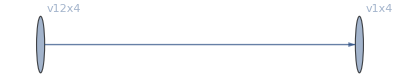

```mathematica
MatchGraph[{v12x4},{v1x4}]
```